```mathematica
geosizefactor=10^12;
geotimefactor=10^18;
TrackColors={"Blue","Red","Green","Magenta"};
Dir=NotebookDirectory[]<>"Track_Data";
Monitor[Tracks=Block[{redtab={},bluetab={},greentab={},magentatab={},NameFile,trcolor},
Do[
Do[NameFile=Dir<>"/"<>TrackColors[[j]]<>"_"<>ToString[i]<>".txt";
If[FileExistsQ[NameFile],trcolor=TrackColors[[j]];Break[];];,{j,TrackColors//Length}];
If[FileExistsQ[NameFile],
If[trcolor=="Red",AppendTo[redtab,Import[NameFile,"Table"]]];
If[trcolor=="Blue",AppendTo[bluetab,Import[NameFile,"Table"]]];
If[trcolor=="Green",AppendTo[greentab,Import[NameFile,"Table"]]];
If[trcolor=="Magenta",AppendTo[magentatab,Import[NameFile,"Table"]]];
]
,{i,0,10^5}];
{redtab,bluetab,greentab,magentatab}
],i];
```

```mathematica
times=10^9/geotimefactor*Sort[Tracks[[3,All,1,4]]];
bins=Join[{0},Table[10^x,{x,-2,0,0.5}],Table[10^x,{x,0.02,3,0.03}]];
counts=BinCounts[times,{bins}];
totcounts=Total[counts];
ΙCe=Table[{(bins[[i]]+bins[[i+1]])/2,1/totcounts*counts[[i]]/(bins[[i+1]]-bins[[i]])},{i,Length[counts]-1}];
```

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False]
```

CheckMachineUnderflow→False

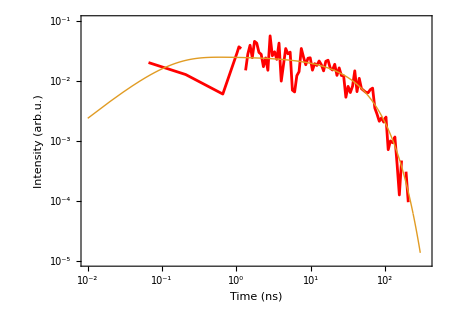

```mathematica
ListLinePlot[{ΙCe,Table[{t,1/(40-0.1)(Exp[-t/40]-Exp[-t/0.1])*HeavisideTheta[t]},{t,10^-2,300,0.01}]},PlotRange->{{10^-2,350},{10^-5,0.1}},ScalingFunctions->{"Log10","Log10"},Frame->True,PlotStyle->{Red,Thick},FrameLabel->{{Style["Intensity (arb.u.)",18,Black,FontFamily->"Times"],None},{Style["Time (ns)",18,Black,FontFamily->"Times"],None}},LabelStyle->{Directive[16],Black,FontFamily->"Times"},AspectRatio->0.7,ImageSize->450]
```

```mathematica
time[t_]:=If[t<10^3,Row[{Round[t,0.001]," fs"}],If[t<10^6,Row[{Round[t*10^-3,0.001]," ps"}],Row[{Round[t*10^-6,0.001]," ns"}]]];
```

```mathematica
0.7(Tracks[[3]]//Length)/(10*10^-3)
```

51030.

```mathematica
xmax=10^9/geosizefactor*Max[Flatten[Tracks[[{1,2,4},All,All,1]],2]];
xmin=10^9/geosizefactor*Min[Flatten[Tracks[[{1,2,4},All,All,1]],2]];
ymax=10^9/geosizefactor*Max[Flatten[Tracks[[{1,2,4},All,All,2]],2]];
ymin=10^9/geosizefactor*Min[Flatten[Tracks[[{1,2,4},All,All,2]],2]];
zmax=10^9/geosizefactor*Max[Flatten[Tracks[[{1,2,4},All,All,3]],2]];
zmin=10^9/geosizefactor*Min[Flatten[Tracks[[{1,2,4},All,All,3]],2]];
```

```mathematica
x=10;
Clear[g];
g=Labeled[Image[Graphics3D[{Table[{Red,Thickness[0.002],Line[10^9/geosizefactor*(Select[Tracks[[1,i]],#[[4]]<10^x &][[All,{1,2,3}]])]},{i,Tracks[[1]]//Length}],Table[{Blue,Thickness[0.002],Line[10^9/geosizefactor*(Select[Tracks[[2,i]],#[[4]]<10^x &][[All,{1,2,3}]])]},{i,Tracks[[2]]//Length}],Table[{Green,Thickness[0.002],Line[10^9/geosizefactor*(Select[Tracks[[3,i]],#[[4]]<10^x &][[All,{1,2,3}]])]},{i,Tracks[[3]]//Length}],Table[{Magenta,Thickness[0.002],Line[10^9/geosizefactor*(Select[Tracks[[4,i]],#[[4]]<10^x &][[All,{1,2,3}]])]},{i,Tracks[[4]]//Length}]},Axes-> True,BoxRatios->{1.0,(ymax-ymin)/(xmax-xmin),(zmax-zmin)/(xmax-xmin)},PlotRange->{{xmin,xmax},{ymin,ymax},{zmin,zmax}},ViewPoint->{-1.4,2.8,0.8},ImageSize->600,LabelStyle->{Directive[16],Black,FontFamily->"Times"},AxesLabel->{Style["X (nm)",18,Black],Style["Y (nm)",18,Black],Style["Z (nm)",18,Black]}]],Text[Style[time[10^15*geotimefactor^-1*10^x],Directive[19],FontFamily->"Times"]],{{Top,Left}}]
```

-Graphics-10. ns

```mathematica
gif=ParallelTable[Labeled[Image[Graphics3D[{Table[{Red,Thickness[0.002],Line[10^9/geosizefactor*(Select[Tracks[[1,i]],#[[4]]<10^x &][[All,{1,2,3}]])]},{i,Tracks[[1]]//Length}],Table[{Blue,Thickness[0.002],Line[10^9/geosizefactor*(Select[Tracks[[2,i]],#[[4]]<10^x &][[All,{1,2,3}]])]},{i,Tracks[[2]]//Length}],Table[{Green,Thickness[0.002],Line[10^9/geosizefactor*(Select[Tracks[[3,i]],#[[4]]<10^x &][[All,{1,2,3}]])]},{i,Tracks[[3]]//Length}],Table[{Magenta,Thickness[0.002],Line[10^9/geosizefactor*(Select[Tracks[[4,i]],#[[4]]<10^x &][[All,{1,2,3}]])]},{i,Tracks[[4]]//Length}]},Axes-> True,BoxRatios->{1.0,(ymax-ymin)/(xmax-xmin),(zmax-zmin)/(xmax-xmin)},PlotRange->{{xmin,xmax},{ymin,ymax},{zmin,zmax}},ViewPoint->{-1.4,2.8,0.8},ImageSize->600,LabelStyle->{Directive[16],Black,FontFamily->"Times"},AxesLabel->{Style["X (nm)",18,Black],Style["Y (nm)",18,Black],Style["Z (nm)",18,Black]}]],Text[Style[time[10^15*geotimefactor^-1*10^x],Directive[19],FontFamily->"Times"]],{{Bottom,Left}}],{x,3,11.5,0.02}];
Export[NotebookDirectory[]<>"Track.gif",gif]
```

/home/yauhenitalochka/mnt/Files/Cpp_projects/LEPAM/Track.gif